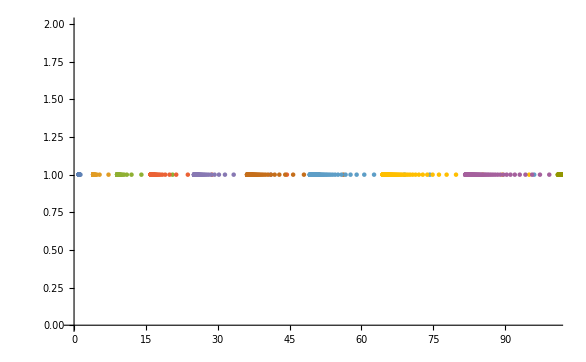

```mathematica
ListPlot[Table[{1/(1/n^2-1/m^2),1},{n,1,10},{m,n+1,100}],PlotRange->{{0,100},{0,2}}]
```

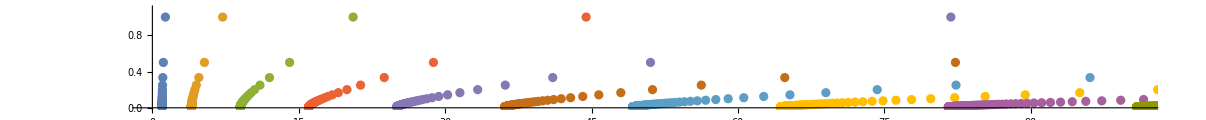

```mathematica
ListPlot[Table[{1/(1/n^2-1/m^2),1/(m-n)},{n,1,10},{m,n+1,n+100}],PlotRange->{{0,101},{0,1.1}},AspectRatio->.1]
```

```mathematica
Flatten[Table[1/m^2-1/n^2,{m,1,10},{n,1,m-1}]]//Sort//N
```

{-0.99,-0.987654,-0.984375,-0.979592,-0.972222,-0.96,-0.9375,-0.888889,-0.75,-0.24,-0.237654,-0.234375,-0.229592,-0.222222,-0.21,-0.1875,-0.138889,-0.101111,-0.0987654,-0.0954861,-0.0907029,-0.0833333,-0.0711111,-0.0525,-0.0501543,-0.0486111,-0.046875,-0.0420918,-0.0347222,-0.03,-0.0276543,-0.024375,-0.0225,-0.0195918,-0.0177778,-0.0154321,-0.0122222,-0.0121528,-0.0104082,-0.00806248,-0.00736961,-0.005625,-0.00478316,-0.00327932,-0.00234568}

```mathematica
Sqrt[13.6/(5.87433*10^-6)]
```

1521.56

```mathematica
1/100^2-1/101^2//N
```

1.9704×10^-6

```mathematica
(2*13.6/(5.87433*10^-6))^(1/3)
```

166.675

```mathematica
Round[13.6/(5.87433*10^-6)]
```

2315158

```mathematica
1/(1/166^2-1/167^2)//Round
```

2307836

```mathematica
1521^2
```

2313441

```mathematica
1522^2
```

2316484

```mathematica
(Sort@Abs@Flatten@(close/@Range[160,1521]))[[;;40]]
```

{8.13916×10^-9,3.03061×10^-8,3.37911×10^-8,4.38456×10^-8,8.90669×10^-8,9.33285×10^-8,1.06654×10^-7,1.20485×10^-7,1.30252×10^-7,1.31864×10^-7,1.68502×10^-7,1.97961×10^-7,2.17118×10^-7,2.18649×10^-7,2.49264×10^-7,2.86179×10^-7,2.94434×10^-7,3.27643×10^-7,3.34285×10^-7,3.73919×10^-7,3.75102×10^-7,4.6634×10^-7,5.50085×10^-7,5.69875×10^-7,6.10237×10^-7,6.146×10^-7,6.4565×10^-7,6.51858×10^-7,7.84028×10^-7,7.86623×10^-7,8.08349×10^-7,8.23208×10^-7,8.32017×10^-7,8.78737×10^-7,9.60822×10^-7,9.6458×10^-7,9.73625×10^-7,1.03843×10^-6,1.1371×10^-6,1.22926×10^-6}

```mathematica
close/@Range[1510,1521]
```

{{-6.4565×10^-7,1.96428×10^-6},{-1.32345×10^-6,9.60822×10^-7},{-2.86179×10^-7,1.68745×10^-6},{-3.34285×10^-7,1.34502×10^-6},{-8.32017×10^-7,5.69875×10^-7},{-9.73625×10^-7,1.68502×10^-7},{-6.51858×10^-7,2.49264×10^-7},{-1.30252×10^-7,5.50085×10^-7},{-3.75102×10^-7,1.06654×10^-7},{-8.90669×10^-8,2.18649×10^-7},{-3.03061×10^-8,1.31864×10^-7},{-4.38456×10^-8,8.13916×10^-9}}

```mathematica
close/@Range[160,170]
```

{{-1.,0.120407},{-1.,0.0997224},{-1.,0.0795443},{-1.,0.0598568},{-1.,0.0406451},{-1.,0.021895},{-1.,0.00359258},{-0.0142753,0.954003},{-0.0317216,0.91952},{-0.0487585,0.885843},{-0.0653981,0.85295}}

```mathematica
find/@Range[160,170]
```

{160.892,161.909,162.926,163.943,164.961,165.978,166.996,168.015,169.033,170.052,171.071}

```mathematica
close[1521]
```

{-4.38456×10^-8,8.13916×10^-9}

```mathematica
find[1521]
```

44665.8

```mathematica
(13.605693/(5.87433*10^-6)#-1)&[1/1521^2-1/44666^2]
```

8.13916×10^-9

```mathematica
(13.605693/(5.87433*10^-6)#-1)&[1/1522^2]
```

-0.00015421

```mathematica
(13.605693/(5.87433*10^-6)#-1)&[1/166^2-1/167^2]
```

0.00359258

```mathematica
(13.605693/(5.87433*10^-6)#-1)&[1/209^2-1/211^2]
```

0.000424066

```mathematica
close/@Range[160,1521]
```

```mathematica
nn=209;
find[nn]-nn
```

1.99914

```mathematica
Round@NN
```

2316127

4.31756×10^-7

4.31755×10^-7